# GWPTools Prototype Engine Examples

Jeremy B. Maddox

Department of Chemistry and Biochemistry
Western Kentucky University
Bowling Green, KY 42101-1079
Email: jeremy.maddox@wku.edu

While the base GWPTools package provides a comprehensive environment for single-component, one-dimensional (1D) Gaussian wavepackets, modeling realistic problems in chemical dynamics and quantum mechanics frequently requires multidimensional coordinate spaces, quantum interference across coherent superpositions, and open-system environmental coupling. This document introduces the suite of analytical prototype engines developed for GWPTools—encompassing two-dimensional wavepackets (GWPEngine2D), two-state and multi-component coherent superpositions (GWPEngineSS1D and GWPEngineMC1D), and one-dimensional open-system reduced density matrices governed by the Caldeira–Leggett master equation (GWPEngineRDM1D). Each extension registers seamlessly into the core GWPTools introspection and property framework, extending exact, closed-form analytical propagation to coupled 2D harmonic surfaces, interfering wavepacket trains, and dissipative thermal relaxation. We illustrate the package loading workflow, metadata introspection queries, constructor syntax, and analytical time evolution across all four prototype wavepacket types.

## Loading the package

Load the GWPTools package. To comply with Wolfram Paclet Repository standards—which prohibit packages from placing symbols in the Global context—all public-facing symbols are scoped under my Wolfram Publisher ID context, MaddoxScience.

```mathematica
Needs["MaddoxScience`GWPTools`"];
```

```mathematica
$ContextPath
```

{MaddoxScience`GWPTools`,System`,Global`}

```mathematica
PacletFind["MaddoxScience/GWPTools"]
```

{PacletObject[…]}

## Introspection

By default, only the single-component 1D wavepacket type is loaded at startup:

```mathematica
GWP["Types"]
```

{1D}

GWP includes built-in introspection queries that are fully documented in the Wolfram Documentation Center (search for GWP in the help bar):

```mathematica
(*Basic introspection*)
GWP["1D"]["Classes"]
GWP["1D"]["Properties","Probabilities"]
```

{DynamicParameters,Energies,ExpectationValues,Probabilities,StaticParameters,Wavefunctions}

{CumulativeDistributionE,CumulativeDistributionP,CumulativeDistributionX,DensityE,DensityP,DensityX,ProbabilityE,ProbabilityP,ProbabilityX}

The interactive table below displays the complete 1D property metadata organized by class. In practice, the ShortKey aliases are particularly convenient for rapid coding. Notice the DynamicClass and StaticClass entries: these govern how a property is evaluated when a “Potential” option is specified (a time-dependent dynamic state) versus omitted (a stationary static state).

```mathematica
(*Inspect all 1D property metadata by class*)TabView[Dataset/@Association@@Rule@@@Transpose@{GWP["1D"]["Classes"],GWP["1D"]["Records",#]&/@GWP["1D"]["Classes"]}]
```

123456

The 1D engine supports several built-in analytical potential models, which are selected via the “Potential” option using the template formats listed below:

```mathematica
Dataset@GWP["PotentialRecords"]
```

Finally, the following table illustrates how each DynamicClass and StaticClass signature determines the calling syntax of the returned property (e.g., a scalar value, a pure function of position [x], a function of time [t], or a space-time function [x, t]):

```mathematica
Dataset[GWP["Signatures"],MaxItems->10]
```

## Static vs. Dynamic 1D Wavepackets

Comprehensive documentation and theoretical Tech Notes for the baseline 1D wavepacket engine are available in the Wolfram Documentation Center (see GWP and GWPObject). The brief examples below review the core constructor and property-query syntax—specifically contrasting stationary (StaticClass) and time-dependent (DynamicClass) evaluations—which serves as the template for all prototype engines in this notebook.

First, we examine a static wavepacket constructed without a “Potential” option:

```mathematica
(*Default 1D GWP with no potential---uses StaticClass*)
obj=GWP["1D"][]
```

GWPObject[…]

```mathematica
(*Spatial probability density and its 1st and 5th spatial derivatives*)
obj["RHOX"][x]
obj["RHOX",1][x]
obj["RHOX",5][x]
```

(ⅇ^(-x^2/2))/(√(2 π))

-(ⅇ^(-x^2/2) x)/(√(2 π))

(ⅇ^(-x^2/2) (-15 x+10 x^3-x^5))/(√(2 π))

Omitting the spatial argument [x] returns the underlying pure Function definition rather than an evaluated algebraic expression (it isn’t broken—just raw!):

```mathematica
obj["RHOX"]
```

Function[{MaddoxScience`GWPTools`GWPDispatcher`Private`var$},Symbol[MaddoxScience`GWPTools`GWPDeveloper`GWP<>1D<>RHOX][0][MaddoxScience`GWPTools`GWPDispatcher`Private`var$][Sequence@@<|GWPType→1D,Parameters→{1/4,0,0,0,0,0,1/(2 π)^(1/4),1,1,{0,0,0},{1/4,0,0,0,0,0,0,0}},Potential→None,PotentialModel→None,Summary→Automatic|>[Parameters]]]

Here is an property BivariateSpatial quantity for calculating the probability of finding the particle between to positions:

```mathematica
(*Interval probability over[x1,x2]*)
obj["PROBX"][x1,x2]
```

1/2 (-1-Erf[x1/(√2)])+1/2 (1+Erf[x2/(√2)])

For a static wavepacket, the wavepacket parameters themselves are returned as constant scalar values. Notice below how RA (real shape) and RX (position center) transition from static values to functions of time [t] once a potential is introduced:

```mathematica
(* GWP parameters *)
obj["RA"]
obj["RX"]
obj["MASS"]
```

1/4

0

1

Next, we evaluate the exact same properties for a dynamic wavepacket by specifying an analytical “Potential” model. Time-dependent properties now accept a time argument t:

```mathematica
(*Displaced coherent state in a harmonic oscillator---uses DynamicClass*)obj=GWP["1D"][1/2,-1,"Potential"->"HO"]
```

GWPObject[…]

```mathematica
(*Time-dependent probability density and spatial derivatives---use Simplify to clean up the symbolic expressions*)
obj["RHOX"][x,t]//Simplify
obj["RHOX",1][x,t]//Simplify
obj["RHOX",5][x,t]//Simplify
```

(ⅇ^(-(x+Cos[t])^2))/(√π)

-(2 ⅇ^(-(x+Cos[t])^2) (x+Cos[t]))/(√π)

-1/(√π)4 ⅇ^(-(x+Cos[t])^2) (x+Cos[t]) (13-16 x^2+8 x^4+8 x (-7+4 x^2) Cos[t]+8 (-2+3 x^2) Cos[2 t]+8 x Cos[3 t]+Cos[4 t])

```mathematica
(*Time-dependent interval probability*)
obj["PROBX"][x1,x2,t]//Simplify
```

1/2 (-Erf[x1+Cos[t]]+Erf[x2+Cos[t]])

```mathematica
(*Dynamic GWP parameters*)
obj["RA"][t]//Simplify (*Constant in time for a coherent state*)
obj["RX"][t]
obj["MASS"]
```

1/2

-Cos[t]

1

## Two-Dimensional Wavepackets (GWPEngine2D)

Next, we load GWPEngine2D to register the “2D” wavepacket type and its associated properties into the active session. A detailed mathematical treatment of the 2D Gaussian ansatz, Heller stability matrix linearization, and normal-mode propagators is available in the Notebooks/TheoryNotes/GWPEngine2D.nb notebook included with the package distribution (which serves as a precursor to a future Wolfram Documentation Center Tech Note).

```mathematica
Needs["MaddoxScience`GWPTools`GWPEngine2D`"]
GWP["Types"]
```

{1D,2D}

Each wavepacket engine defines its own set of properties and analytical potential models. As prototype extensions, the multi-dimensional and multi-component engines currently implement a streamlined core subset of the full 1D property library:

```mathematica
(*Inspect all 2D properties by class*)TabView[Dataset/@Association@@Rule@@@Transpose@{GWP["2D"]["Classes"],GWP["2D"]["Records",#]&/@GWP["2D"]["Classes"]}]
```

123456

```mathematica
Dataset@GWP["2D"]["PotentialRecords"]
```

Below is a static, fully symbolic 2D wavepacket. The positional arguments are the two-by-two symmetric shape matrix, the position center vector, the momentum center vector, and the complex scalar phase, followed by optional “HBAR” and “MASS” rules:

```mathematica
obj=GWP["2D"][{{RAXX+I*IAXX,RAXY+I*IAXY},{RAXY+I*IAXY,RAYY+IAYY}},{RX,RY},{RPX,RPY},RG+I*IG,"HBAR"->HBAR,"MASS"->MASS]
```

GWPObject[…]

```mathematica
(*Coordinate-space wavefunction*)
obj["PSIX"][x,y]
```

ⅇ^(IG/HBAR+(-ⅈ IAXX-RAXX) (-RX+x)^2-2 (ⅈ IAXY+RAXY) (-RX+x) (-RY+y)-(IAYY+RAYY) (-RY+y)^2+(ⅈ (ⅈ IG+RG+RPX (-RX+x)+RPY (-RY+y)))/HBAR) √(2/π) (-RAXY^2+RAXX (IAYY+RAYY))^(1/4)

```mathematica
(*Spatial probability density*)
obj["RHOX"][x,y]
```

(2 ⅇ^(-2 RAXX (-RX+x)^2-4 RAXY (-RX+x) (-RY+y)-2 (IAYY+RAYY) (-RY+y)^2) √(-RAXY^2+RAXX (IAYY+RAYY)))/π

Next, we initialize a dynamic 2D wavepacket in an uncoupled isotropic harmonic oscillator (“Potential” -> “HO” with standard parameters (m=1, ℏ=1, ω_x=ω_y=1) using a diagonal real shape matrix and an initial displacement along x. Because the ground-state Gaussian width parameter is 1/2, this state is a displaced coherent state along x ( α_(x x,0)=1/2) and a stretched/squeezed state along y (α_(y y,0)=1/4). Omitting the trailing momentum center and phase arguments defaults them to zero:

```mathematica
(* GWP 2D *)
obj=GWP["2D"][{{1/2,0},{0,1/4}},{1,0},"Potential"->"HO"]
```

GWPObject[…]

Querying the potential energy surface, time-dependent probability density, and coordinate uncertainties along x and y:

```mathematica
(*Potential energy surface for "HO"*)
obj["PEX"][x,y,t]
```

x^2/2+y^2/2

```mathematica
(*Time-dependent probability density*)
rho=obj["RHOX"][x,y,t]//Simplify
```

(2 ⅇ^(-(x-Cos[t])^2-(4 y^2)/(5+3 Cos[2 t])) √(1/(5+3 Cos[2 t])))/π

```mathematica
(*Position uncertainties along x (stationary) and y (breathing)*)
obj["UX"][t]
obj["UY"][t]
```

1/(√2)

1/2 √(4 Cos[t]^2+Sin[t]^2)

Evaluate the cell below to animate the 2D probability density over one trap period (showing classical oscillation along x combined with symmetric width breathing along y):

```mathematica
ListAnimate[Table[Plot3D[rho,{x,-3,3},{y,-3,3},PlotRange->{0,1}],{t,0,2Pi,2Pi/100}]]
```

Finally, we demonstrate the parameterized “Harmonic” potential model {“Harmonic”, omegaX, omegaY, omegaXY} with strong bilinear mode coupling ( ω_(x y)=7/8):

```mathematica
obj=GWP["2D"][{{1/2,0},{0,1/4}},{-1,0},{0,-2},"Potential"->{"Harmonic",1,1,7/8}]
```

GWPObject[…]

```mathematica
pot=obj["PEX"][x,y,t]
```

x^2/2+(49 x y)/64+y^2/2

```mathematica
Plot3D[pot,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
rho2=obj["RHOX"][x,y,t];
```

```mathematica
ListAnimate[Table[Plot3D[rho2,{x,-5,5},{y,-5,5},PlotRange->{0,1}],{t,0,4Pi,4Pi/100}]]
```

## 1D Superposition states (GWPEngineSS1D)

The GWPEngineSS1D sub-package registers the “SS1D” wavepacket type, which constructs a coherent two-term superposition of arbitrary 1D Gaussian wavepackets.

```mathematica
Needs["MaddoxScience`GWPTools`GWPEngineSS1D`"]
GWP["Types"]
```

{1D,2D,SS1D}

Currently, SS1D implements a focused set of coordinate-space wavefunction and probability properties:

```mathematica
GWP["SS1D"]["Properties"]
```

{ConjugateWavefunctionX,CumulativeDistributionX,DensityX,Normalization,WavefunctionX}

However, it inherits the complete library of analytical potential models from the base 1D engine:

```mathematica
GWP["SS1D"]["PotentialNames"]
```

{Free,Harmonic,HO,Linear,LinearForcedHO,NonResonantForcedHO,ParabolicBarrier,ResonantForcedHO}

The positional constructor arguments mirror those of GWP[“1D”], except each parameter is passed as a two-element list {param1, param2} representing the two Gaussian branches. An additional option, “C”, specifies the complex relative weight of the second wavepacket with respect to the first:

```mathematica
obj=GWP["SS1D"][{RA1+I*IA1,RA2+I*IA2},{RX1,RX2},{RP1,RP2},{RG1+I*IG1,RG2+I*IG2},"C"->RC+I*IC,"MASS"->MASS,"HBAR"->HBAR]
```

GWPObject[…]

```mathematica
(*Symbolic wavefunction for two equal-width Gaussians centered at x1 and x2*)GWP["SS1D"][{1,1},{x1,x2},"C"->c]["PSIX"][x]
```

(ⅇ^(-(x-x1)^2) (2/π)^(1/4)+c ⅇ^(-(x-x2)^2) (2/π)^(1/4))/(√(1+c^2+2 c ⅇ^(-1/2 (x1-x2)^2)))

Varying the relative mixing coefficient “C” controls the quantum interference between the two components. Below, we compare symmetric (“C” -> 1, constructive interference) and antisymmetric (“C” -> -1, destructive node at the origin) superpositions using the default initial state parameters, followed by an asymmetric two-Gaussian superposition with a complex relative phase (“C” -> Exp[I*Pi/3]):

```mathematica
rho1=GWP["SS1D"]["C"->1]["RHOX"][x];
rho2=GWP["SS1D"]["C"->-1]["RHOX"][x];
```

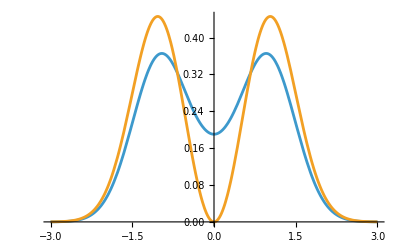

```mathematica
Plot[{rho1,rho2},{x,-3,3}]
```

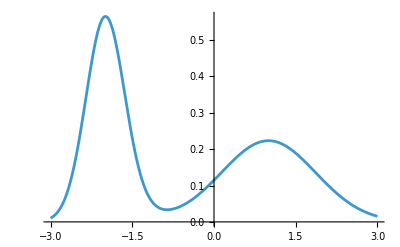

```mathematica
rho3=GWP["SS1D"][{2,1/3},{-2,1},"C"->Exp[I*Pi/3]]["RHOX"][x];
Plot[rho3,{x,-3,3}]
```

Finally, a classic dynamical example—a coherent superposition of a displaced coherent state (x_(1,0)=-5) and the stationary ground state (x_(2,0)=0) in a harmonic oscillator (“Potential” -> “HO”)—shows the displaced branch sweeping periodically through the stationary ground state and generating transient interference fringes at every collision:

```mathematica
rho4=GWP["SS1D"][{1/2,1/2},{-5,0},"Potential"->"HO"]["RHOX"][x,t];
```

```mathematica
ListAnimate[Table[Plot[rho4,{x,-6,6},PlotRange->{0,1}],{t,0,2Pi,2Pi/100}]]
```

## 1D Multi-Component Superpositions (GWPEngineMC1D)

The GWPEngineMC1D sub-package generalizes and supersedes SS1D by constructing coherent superpositions of an arbitrary number N of 1D Gaussian wavepacket components:

```mathematica
Needs["MaddoxScience`GWPTools`GWPEngineMC1D`"]
GWP["Types"]
```

{1D,2D,SS1D,MC1D}

Like SS1D, this prototype engine currently implements a focused set of coordinate-space properties while supporting all analytical potential models from the base 1D library—providing a flexible foundation for multi-state wavepacket trains and basis-set expansions:

```mathematica
GWP["MC1D"]["Properties"]
GWP["MC1D"]["PotentialNames"]
```

{ConjugateWavefunctionX,CumulativeDistributionX,DensityX,Normalization,WavefunctionX}

{Free,HO}

Calling GWP[“MC1D”][] with no arguments initializes a default two-component state, while passing $N$-element parameter lists along with the weight option “C” -> {c1, c2, ..., cN} constructs an $N$-state superposition. Below, we initialize and plot the spatial probability density of a symmetric three-component Gaussian wavepacket train centered at x_0∈{-3,0,3}:

```mathematica
obj=GWP["MC1D"][]
```

GWPObject[…]

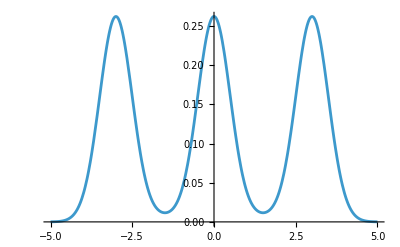

```mathematica
Plot[GWP["MC1D"][{1,1,1},{-3,0,3},"C"->{1,1,1}]["RHOX"][x],{x,-5,5}]
```

## Open-System Reduced Density Matrices (GWPEngineRDM1D)

Finally, we load GWPEngineRDM1D to register the “RDM1D” wavepacket type, which extends GWPTools from pure-state wavefunctions to mixed-state Gaussian reduced density matrices $\rho(x, x’, t)$. (Extensive theoretical notes and derivations for this engine are available in Notebooks/TheoryNotes/GWPEngineRDM1D.nb.

```mathematica
Needs["MaddoxScience`GWPTools`GWPEngineRDM1D`"]
GWP["Types"]
```

{1D,2D,SS1D,MC1D,RDM1D}

Alongside the standard unitary potential models, RDM1D introduces analytical open-system potential models—such as “HarmonicCL”—governed by the Caldeira–Leggett master equation:

```mathematica
Dataset@GWP["RDM1D"]["PotentialRecords"]
```

Below, we initialize a displaced and stretched Gaussian density matrix ( α_0=1/4, x_0=1) in a harmonic oscillator coupled to an Ohmic thermal reservoir using “Potential” -> {“HarmonicCL”, omega, gamma, kT} with ω=1, γ_d=1/4, k_B T=2. Omitting the trailing momentum center, phase, and initial thermal decoherence parameter θ_0 defaults them to zero:

```mathematica
obj=GWP["RDM1D"][1/4,1,"Potential"->{"HarmonicCL",1,1/4,2}]
```

GWPObject[…]

Unlike the isolated unitary harmonic oscillator, environmental friction and thermal diffusion damp the classical trajectory and width breathing over time, relaxing both the real shape parameter RA and the diagonal spatial probability density RHOX (ρ(x,x,t)) toward a stationary thermal Gibbs distribution:

```mathematica
(*Visualize dissipative relaxation of the spatial probability density*)Plot3D[obj["RHOX"][x,t],{t,0,4*2*Pi},{x,-5,5},PlotRange->All,PlotPoints->50,AxesLabel->{"time","position","density"},BaseStyle->FontSize->12]
```

-Graphics3D-

```mathematica
(*Analytical time-dependent real shape parameter and diagonal density*)
obj["RA"][t]
obj["RHOX"][x,t]
```

(63 ⅇ^(t/4))/(128 (-11/4+(63 ⅇ^(t/4))/16+25/32 Cos[(3 √7 t)/4]-3/32 √7 Sin[(3 √7 t)/4]))

3/8 ⅇ^(-(63 ⅇ^(t/4) (x-ⅇ^(-t/8) (Cos[(3 √7 t)/8]+Sin[(3 √7 t)/8]/(3 √7)))^2)/(64 (-11/4+(63 ⅇ^(t/4))/16+25/32 Cos[(3 √7 t)/4]-3/32 √7 Sin[(3 √7 t)/4]))) √(7/π) √(ⅇ^(t/4)/(-11/4+(63 ⅇ^(t/4))/16+25/32 Cos[(3 √7 t)/4]-3/32 √7 Sin[(3 √7 t)/4]))

URLRead::invhttp: Could not resolve host: www.wolframcloud.com.